```mathematica
ListaC={ {0,19},
{1,41},{2,40},{3,27},
{4,21},{5,10},{6,8},{7,9},{8,7},{9,12},{10,3},{11,3},{12,4},{13,8},{14,9},{15,13},{16,12},{17,11},{18,9},{19,15},
{20,18},{21,14},{22,14},{23,18},{24,22},{25,22},{26,13},{27,19},{28,26},{29,23},{30,26},{31,30},{32,52},{33,41},{34,46},{35,45},{36,65},{37,66},{38,92},{39,88},{40,104},{41,126},{42,136},{43,176},{44,180},{45,192},{46,208},{47,251},{48,279},{49,322},{50,349},{51,399},{52,474},{53,470},{54,525},{55,604},{56,681},{57,686},{58,750},{59,788},{60,842},{61,874},{62,939},{63,972},{64,958},{65,1070},{66,1096},{67,1171},{68,1195},{69,1230},{70,1220},{71,1140},{72,1216},{73,1208},{74,1209},{75,1270},{76,1280},{77,1128},{78,1175},{79,1126},{80,1082},{81,1052},{82,986},{83,935},{84,841},{85,743},{86,651},{87,578},{88,528},{89,392},{90,361},{91,311},{92,254},{93,170},{94,139},{95,86},{96,82},{97,42},{98,33},{99,14},{100,17},{101,9},{102,5},{103,4},{104,2},{105,1},{106,1},{108,1},{110,1},{113,1}};
```

```mathematica
N[Kurtosis[ListaC]]
```

{1.81693,2.17923}

```mathematica
L=Length[ListaC]
```

110

```mathematica
∑_(j=1)^L ListaC[[j]][[2]]
```

40362

```mathematica
μ=∑_(j=1)^L ((ListaC[[j]][[1]]*ListaC[[j]][[2]])/40362.)
```

69.0852

```mathematica
σ=√(∑_(j=1)^L (((ListaC[[j]][[1]]-μ)^2*ListaC[[j]][[2]])/40361.))
```

13.7601

```mathematica
σ^2
```

189.342

```mathematica
Subscript[CA, F]=∑_(j=1)^L (((ListaC[[j]][[1]]-μ)^3*ListaC[[j]][[2]])/(40362*σ^3))
```

-0.972396

```mathematica
K=∑_(j=1)^L (((ListaC[[j]][[1]]-μ)^4*ListaC[[j]][[2]])/(40362*σ^4))-3
```

2.39587

```mathematica
Length[ListaC]
```

110

```mathematica
Lista2=Table[{ListaC[[j]][[1]],(ListaC[[j]][[2]])/40362},{j,1,Length[ListaC]}];
```

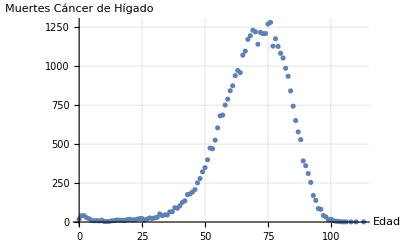

```mathematica
g1=ListPlot[ListaC ,GridLines->Automatic,AxesLabel->{"Edad","Muertes Cáncer de Hígado"}]
```

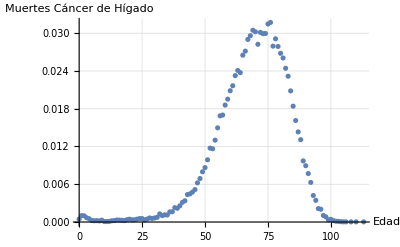

```mathematica
g3=ListPlot[Lista2 ,GridLines->Automatic,AxesLabel->{"Edad","Muertes Cáncer de Hígado"}]
```

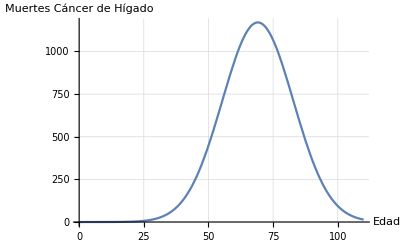

```mathematica
g2=Plot[40362*1/(√(2π)σ) ⅇ^(-(x-μ)^2/(2 σ^2)),{x,0,110},GridLines->Automatic,AxesLabel->{"Edad","Muertes Cáncer de Hígado"}]
```

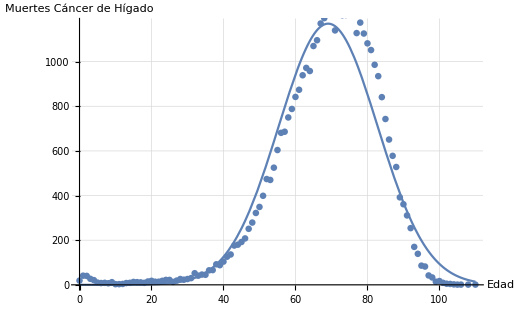

```mathematica
Show[g2,g1]
```

```mathematica
Kurtosis[40362*1/(√(2π)σ) ⅇ^(-(x-μ)^2/(2 σ^2))]
```

Kurtosis[1170.21 ⅇ^(-0.0026408 (-69.0852+x)^2)]